```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Für komplexzahlige Nullstellen gilt:

f(z_0)=0=0·ⅇ^(ⅉ φ) , φ∈ℝ

Wird das Argument der komplexzahligen Funktion in Form eines Äquiphasenwinkeldiagramms (ContourPlot[…]) aufgetragen, lassen sich die Nullstellen wie folgt daraus ablesen:
Die Linien stellen jeweils einen Wert des Phasenwinkels dar und enden demnach gemeinsam in einem Punkt bzw. der Nullstelle. Der Übersichtlichkeit halber werden diese Linien ausgeblendet (Contours→0), sodass die Enden der weißen Linien den Nullstellen entsprechen.
Die so abgelesenen Nullstellen können ggf. als Startpunkte für ein numerisches Iterationsverfahren dienen. Im folgenden Programm wird das Newton’sche Verfahren (FindRoot[…]) verwendet.

## Eingabe (f(z))

```mathematica
ClearAll["Global`*"]
f[z_]=z^5-Exp[I z];
```

## Äquiphasenwinkeldiagramm

```mathematica
𝓀𝓇ℯ𝒾𝓈ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉={0,0};
kreisRadius=2;
```

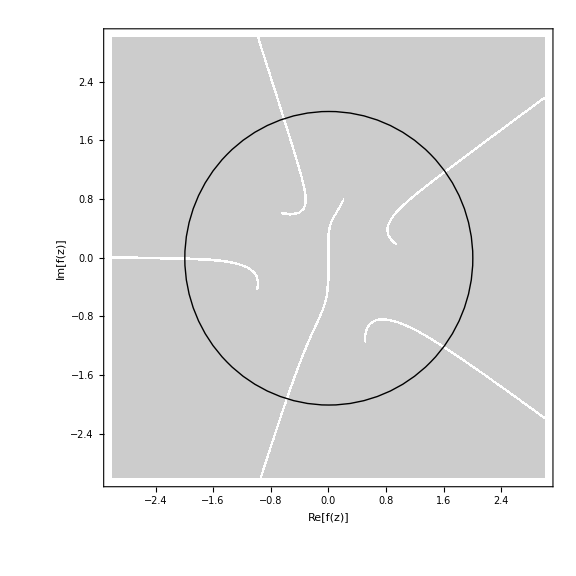

```mathematica
(*Ausgabe*)
𝓍ℬℯ𝓇ℯ𝒾𝒸𝒽={𝓀𝓇ℯ𝒾𝓈ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]]-kreisRadius,𝓀𝓇ℯ𝒾𝓈ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]]+ kreisRadius};
𝓎ℬℯ𝓇ℯ𝒾𝒸𝒽={𝓀𝓇ℯ𝒾𝓈ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]]-kreisRadius,𝓀𝓇ℯ𝒾𝓈ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]]+ kreisRadius};
plot=ContourPlot[
Arg[f[x+I y]],{x,-1+𝓍ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],1+𝓍ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]},{y,-1+𝓎ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],1+𝓎ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]},
Contours->0,FrameLabel->{"Re[f(z)]","Im[f(z)]"},FrameTicks-> All,GridLines->Full,ImageSize->Large];
kreis=Graphics[Circle[𝓀𝓇ℯ𝒾𝓈ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉,kreisRadius]];
Print[Show[plot,kreis]]
```

## Programm (automatisch)

```mathematica
Δ=10^-1;
```

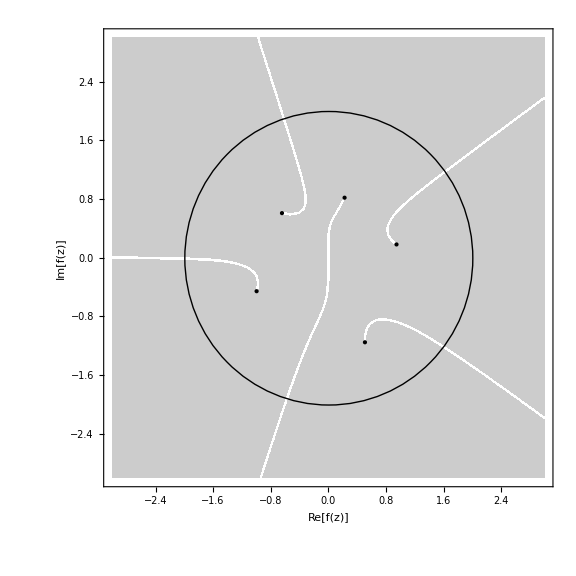

𝓏_0 = (-0.996125-0.455751 ⅈ
-0.643628+0.608126 ⅈ
0.22566+0.818464 ⅈ
0.947089+0.181572 ⅈ
0.508653-1.15171 ⅈ)
→ Probe erfolgreich ☺

```mathematica
(*Programm*)
Off[FindRoot::reged]
Off[FindRoot::lstol]
𝓏ℬℯ𝓇ℯ𝒾𝒸𝒽={-1+𝓍ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]]+I (-1+𝓎ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]]),1+𝓍ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]+I (1+𝓎ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]])};
𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽=Select[
DeleteDuplicates[Flatten[Table[
Round[FindRoot[f[z],{z,x+I y,𝓏ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓏ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]}][[1,2]],N[10^-12]],
{x,𝓍ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓍ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]],Δ},{y,𝓎ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓎ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]],Δ}]]],
Abs[Re[#]-𝓀𝓇ℯ𝒾𝓈ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[1]]+I(Im[#]-𝓀𝓇ℯ𝒾𝓈ℳ𝒾𝓉𝓉ℯℓ𝓅𝓊𝓃𝓀𝓉[[2]])]≤kreisRadius&];

(*Ausgabe*)
𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒫𝓊𝓃𝓀𝓉ℯ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽=Table[
Graphics[{PointSize->Medium,Point[{Re[𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽[[i]]],Im[𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽[[i]]]}]}],
{i,1,Length[𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽]}];
Print[Show[plot,kreis,𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒫𝓊𝓃𝓀𝓉ℯ𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽]]
Print[StringForm["𝓏_0 = ``\n``",
𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽//MatrixForm,
If[AllTrue[Table[Chop[f[z]/.z->𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽[[i]]]== 0,{i,Length[𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒜𝓊𝓉ℴ𝓂𝒶𝓉𝒾𝓈𝒸𝒽]}],TrueQ],
Style["→ Probe erfolgreich ☺",Darker[Green]],Style["→ Fehler aufgetreten ☹",Darker[Red]]]]]
```

## Programm (manuell)

```mathematica
𝓏𝒮𝓉𝒶𝓇𝓉={-1-.4I,.4-1.2I,1+.2I,.2+.8 I,-.6+.6I};
```

```mathematica
(*Programm*)
𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃ℳ𝒶𝓃𝓊ℯℓℓ=Table[
FindRoot[f[z],{z,𝓏𝒮𝓉𝒶𝓇𝓉[[i]]}][[1,2]],
{i,1,Length[𝓏𝒮𝓉𝒶𝓇𝓉]}];

(*Ausgabe*)
𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒫𝓊𝓃𝓀𝓉ℯℳ𝒶𝓃𝓊ℯℓℓ=Table[
Graphics[{PointSize->Medium,Point[{Re[𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃ℳ𝒶𝓃𝓊ℯℓℓ[[i]]],Im[𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃ℳ𝒶𝓃𝓊ℯℓℓ[[i]]]}]}],
{i,1,Length[𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃ℳ𝒶𝓃𝓊ℯℓℓ]}];
Print[Show[plot,kreis,𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃𝒫𝓊𝓃𝓀𝓉ℯℳ𝒶𝓃𝓊ℯℓℓ]]
Print[StringForm["𝓏_0 = ``\n``",
𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃ℳ𝒶𝓃𝓊ℯℓℓ//MatrixForm,
If[AllTrue[Table[Chop[f[z]/.z->𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃ℳ𝒶𝓃𝓊ℯℓℓ[[i]]]==0,{i,Length[𝓃𝓊ℓℓ𝓈𝓉ℯℓℓℯ𝓃ℳ𝒶𝓃𝓊ℯℓℓ]}],TrueQ],
Style["→ Probe erfolgreich ☺",Darker[Green]],Style["→ Fehler aufgetreten ☹",Darker[Red]]]]]
```

-Graphics-

𝓏_0 = (-0.996125-0.455751 ⅈ
0.508653-1.15171 ⅈ
0.947089+0.181572 ⅈ
0.22566+0.818464 ⅈ
-0.643628+0.608126 ⅈ)
→ Probe erfolgreich ☺